# Gallery of mathematical images

### Author

Bernd Thaller
Institute for Mathematics and Scientific Computing
University of Graz
Austria

### Source

http://www.uni-graz.at/imawww/vqm/

### Abstract

Mathematica source code for the images at  http://www.uni-graz.at/imawww/vqm/pages/colorgallery/index.html

In this notebook, the value of the option PlotPoints has been reduced for performance reasons.

```mathematica
$starttime=AbsoluteTime[];
{$Version, Date[]}
```

{11.3.0 for Microsoft Windows (64-bit) (March 7, 2018),{2018,4,24,23,0,27.5023235}}

## Load package

```mathematica
Needs["VQM`ComplexPlot`"]
```

## 01: alien1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ab],1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Exp[Tan[y+I x]],{x,-π/3,π/3},{y,0,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 02: alien2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ab],1/(1+ar^2),1/(1+ar^2)]];QComplexDensityPlot[Zeta[Zeta[y+I x]],{x,-.5,.5},{y,.5,1.2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 03: alien3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ab],1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Exp[x+I y]^Tan[y+I x],{x,-π/8,π/4},{y,π+0.0001,(15 π)/8},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 04: alien4

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[√ab],1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Exp[x+I y]^Tan[y+I x],{x,-π/9,(5 π)/12},{y,π+0.0001,(14 π)/8},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 05: butterfly

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(1+ab^2),1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Sin[Sin[1/(y+I x)]],{x,-1,1},{y,-.5,.5},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False];
```

## 06: crossing1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(1+ab^2),1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Cot[x+I y]^Tan[y+I x],{x,-(5 π)/4,3 π-(5 π)/4},{y,-π,2 π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 07: crossing2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ab],1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[E^(Tan[x+I y] Tan[y+I x]),{x,-2 π,2 π},{y,-2 π,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 08: crossing3

```mathematica
QComplexDensityPlot[E^(Tan[x+I y] Tan[y+I x]),{x,-2 π,2 π},{y,-2 π,π},PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 09: flames1

```mathematica
Remove[myColorMap];
myColorMap=Function[{ab,ar},Hue[1/(1+ab^2),1/(1+ar^2),1-(.8)/(1+ab^2)]];
QComplexDensityPlot[Sin[Sin[Tan[-y+I x]]],{x,-2,2},{y,-2.5,1},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 10: flames2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(1+ab^2),1/(1+ar^2),1-(.8)/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[Sin[Sin[Log[-y+I x]]],{x,-20,20},{y,-20,20},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 11: flowers1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Cos[ar]^4,Sin[ar]^2,Cos[ab]^2]];
```

```mathematica
QComplexDensityPlot[1/((1-1/(1-Sin[x+I y])^2)^2),{x,-π/2,(3 π)/2},{y,-(3 π)/4,(3 π)/4},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 12: flowers2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(1+ar^2),1/(1+ab^2),1/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[1/((1-1/(1-Sin[x+I y])^2)^2),{x,-π/2,(11 π)/2},{y,-π,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 13: flowers3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Mod[ar,1],Mod[ab,1],Mod[ar,1]]];
```

```mathematica
QComplexDensityPlot[1/((1-1/(1-Sin[x+I y])^2)^2),{x,-1.5,2.5},{y,-1.5,2.5},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 14: flowers4

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Mod[ab,1],Mod[ab,1],Mod[ar,1]]];
```

```mathematica
QComplexDensityPlot[1/((1-1/(1-Sin[x+I y])^2)^2),{x,-2,6},{y,-2.2,3.3},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 15: flowers5

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},RGBColor[(.6)/(1+ar^2)+(.4)/(1+ab^2),(.4)/(1+ar^2)+(.6)/(1+ab^2),(.1)/(1+ar^2)+(.9)/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[Sin[1/((1-1/(1-Sin[x+I y])^2)^2)]^2,{x,-π/2,(3 π)/2},{y,-(3 π)/4,(3 π)/4},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 16: flowers6

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,1/(1+ar^2)];
```

```mathematica
QComplexDensityPlot[Log[Sin[1/(y+I x)^5]],{x,-1.5,1.5},{y,-1.5,1.5},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 17: flowers7

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,(.3)/(1+ar^2)+.7 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Log[Sin[Log[(x+I y)^7]]],{x,-π,π},{y,-π,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 18: flowers8

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Log[Sin[1/(x+I y)^3]],{x,-π/2,π/2},{y,-π/2,π/2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 19: flowers9

```mathematica
Remove[myColorMap];
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
QComplexDensityPlot[Log[Sin[1/(x+I y)^11]],{x,-π/2,π/2},{y,-π/2,π/2},QComplexToColorMap->myColorMap,PlotPoints->150,Mesh->False,Frame->False,Compiled->False]
```

-Graphics-

## 20: fractal1

```mathematica
Remove[mandelbrot];
```

```mathematica
mandelbrot=Compile[{{k,_Complex}},Module[{val=0+0 I,cnt=0},While[Re[val]^2+Im[val]^2<15000&&cnt<100,val=val^2+k;cnt++];cnt Exp[I Arg[val]]]];
```

```mathematica
Timing[QComplexDensityPlot[mandelbrot[x+I y],{x,-2.6,1.4},{y,-2,2},PlotPoints->100,Mesh->False,Compiled->False,QSphereRadius->10,QLightnessRange->{0,0.9}]]
```

{0.140625,-Graphics-}

## 21: fractal2

```mathematica
Remove[mandelbrot];
```

```mathematica
mandelbrot=Compile[{{k,_Complex}},Module[{val=0+0 I,cnt=0},While[Re[val]^2+Im[val]^2<15000&&cnt<100,val=val^2+k;cnt++];cnt Exp[I Arg[val]]]];
```

```mathematica
QComplexDensityPlot[mandelbrot[x+I y],{x,-1.49,-1.47},{y,-0.01,0.01},Compiled->False,PlotPoints->100,Mesh->False,QSphereRadius->50,QValueRange->{15,110}]
```

-Graphics-

## 22: kitchen1

```mathematica
Remove[f,g,myColorMap];
```

```mathematica
f[x_]:=1-x^2;
```

```mathematica
g=Compile[{{x,_Complex}},Simplify[Nest[f,x,5]]];
```

```mathematica
myColorMap=Function[{ab,ar},RGBColor[Mod[Log[ab+1.],1],Mod[Log[Log[ab+1.]],1],Mod[.8 ar,1]]];
```

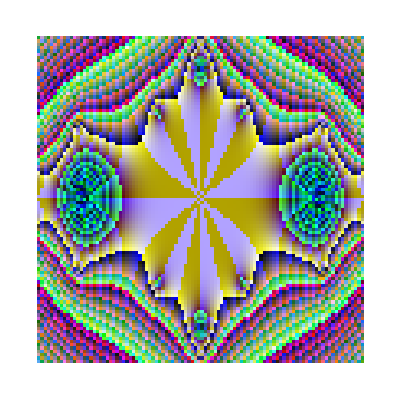

```mathematica
QComplexDensityPlot[g[x+I y],{x,-1.4,1.4},{y,-.8,.8},Compiled->False,QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

## 23: kitchen2

```mathematica
Remove[f,g,h,myColorMap];
```

```mathematica
f[x_,y_]=1/((x+I y)^5-1);
```

```mathematica
g[x_,y_]=Simplify[f[f[x,y],1/f[x,y]]];
```

```mathematica
h=Compile[{{x,_Complex},y},g[x,y]];
```

```mathematica
myColorMap[ab_,ar_]=Hue[5 ab,1/2 (1+Sin[ar/π]),1/2 (1+Cos[ar/π])];
```

```mathematica
QComplexDensityPlot[h[x,y],{x,-1.4,1.4},{y,-1.4,1.4},Compiled->False,QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 24: quantum1

```mathematica
Remove[Gauss,p0,f,doplot];
```

```mathematica
Gauss[x_,t_,a_,x0_,p0_]:=(√(a/π) Exp[-((a x.x)/2-I p0.x+1/2 I t p0.p0)/(1+I t a)])/(1+I t a);
```

```mathematica
p0={2,2.};
```

```mathematica
f[x_,y_,t_]:=Gauss[{x,y},t,1/2,x0,p0];
```

```mathematica
doplot[t_,opts___]:=QComplexDensityPlot[Exp[I 10 Sin[3 x] Cos[3 y]] f[x,y,t],{x,-5.5,5.5},{y,-5.5,5.5},opts,Mesh->False,Frame->False,QSphereRadius->.5,PlotPoints->100];
```

```mathematica
doplot[-.8,QLightnessRange->{.4,.4}]
```

-Graphics-

## 25: quantum2

```mathematica
Remove[Gauss,p0,f,myColorMap,doplot];
```

```mathematica
Gauss[x_,t_,a_,x0_,p0_]:=(√(a/π) Exp[-((a x.x)/2-I p0.x+1/2 I t p0.p0)/(1+I t a)])/(1+I t a);
```

```mathematica
p0={2,2.};
```

```mathematica
f[x_,y_,t_]:=Gauss[{x,y},t,1/2,x0,p0];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[1-ab]/(1+ar^2),1/(1+ab^2),1/(1+ar^2)]];
```

```mathematica
doplot[t_]:=QComplexDensityPlot[Exp[I 12 Sin[3 x] Cos[3 y]] f[x,y,t],{x,-4,3},{y,-4,3},Mesh->False,Frame->False,QComplexToColorMap->myColorMap,PlotPoints->100]
```

```mathematica
doplot[-.3]
```

-Graphics-

## 26: satin1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ab],1-(.8)/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[LegendreP[5,LegendreP[5,x+I y]],{x,-1,1},{y,-.5,.5},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 27: satin2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Cos[ab+.7],(.5)/(1+ar^2)+(.5)/(1+ab^2),(.7)/(1+ar^2)+(.3)/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[LegendreP[5,LegendreP[4,x+I y]],{x,-1,1},{y,-.3,.3},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 28: satin3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1-1/(1+ab^2),1-(.8)/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Zeta[Zeta[y+I x]],{x,-.15,.15},{y,.84,1.01},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 29: sinsin1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Sin[ar]^2,Mod[ab,1],Mod[ar,1]]];
```

```mathematica
QComplexDensityPlot[Sin[Sin[x+I y]],{x,-π-0.6,0.6},{y,-π/2-0.6,π/2+0.6},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 30: sinsin2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Mod[ab,1],Mod[ar,1],Mod[ar,1]]];
```

```mathematica
QComplexDensityPlot[Sin[Sin[x+I y]],{x,-π,π},{y,-π,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 31: sinsin3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},RGBColor[Cos[ab]^2,(.5)/(1+ar^2)+(.5)/(1+ab^2),(.7)/(1+ar^2)+(.3)/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[Sin[2 Sin[2 (x+I y)]],{x,-π/2,π},{y,-1,1},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 32: spider1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(ab^2+1),1/(ar^2+1),1/(ar^2+1)]];
```

```mathematica
QComplexDensityPlot[Sin[x+I y]^Sin[x+I y],{x,-π/2,(3 π)/2},{y,-π,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 33: spider2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},RGBColor[(.8)/(1+ar^2)+(.2)/(1+ab^2),(.2)/(1+ar^2)+(.8)/(1+ab^2),(.5)/(1+ar^2)+(.5)/(1+ab^2)]];
```

```mathematica
QComplexDensityPlot[Sin[2 Sin[2 (x+I y)]],{x,-π/2,π},{y,-2,2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 34: spider3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Log[Log[Log[Sin[1/(x+I y)]]]],{y,-.3,.3},{x,-.2,.2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 35: spider4

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Log[Log[Log[Sin[1/(x+I y)]]]],{y,-.5,.5},{x,-.3,.7},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 36: spider5

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[ar,.8 Sin[Log[ab]]^2+.2 Cos[Log[ab]]^2,(.1)/(1+ab^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Log[Log[Log[Sin[1/(x+I y)]]]],{y,-.5,.5},{x,-.3,.7},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 37: spider6

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[Sin[ar],Sin[ab]^2,Cos[ar]^2];
```

```mathematica
QComplexDensityPlot[Log[Log[Log[Sin[1/(x+I y)]]]],{y,-.5,.5},{x,-.3,.4},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 38: tantan1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Mod[ab,1],Mod[ab,1],1.-3/4 Mod[ar/2,1]]];
```

```mathematica
QComplexDensityPlot[Tan[Tan[x+I y]],{x,-π/2,π},{y,-π/2,π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 39: tantan2

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1-ab,Mod[ab,1],1.-1/4 3.5 Mod[ar/2,1]]];
```

```mathematica
QComplexDensityPlot[Tan[Tan[x+I y]],{x,π/8,π+0.01},{y,-π/3,π/2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 40 tantan3

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1-ab,Mod[ab 2,1],1.-1/4 3.5 Mod[ar/2,1]]];
```

```mathematica
QComplexDensityPlot[Tan[Tan[x+I y]],{x,π/2,π/2+π/8},{y,-π/16,π/16},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 41 tantan4

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[Cos[ab]^2,Mod[ab 3,1],1.-3/4 Mod[ar 2,1]]];
```

```mathematica
QComplexDensityPlot[Tan[Tan[x+I y]],{x,π/2,π},{y,-π/5,π/5},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 42 waves1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap=Function[{ab,ar},Hue[1/(1+ab^2),1/(1+ar^2),1/(1+ar^2)]];
```

```mathematica
QComplexDensityPlot[Sin[x+I y]^Tan[y+I x],{x,-π/2,π},{y,-2 π,6 π},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 43: logsine

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=
		Hue[.52+1/(1+ab^2),Sin[Log[ab]]^2,1/(1+ar^2)];
```

```mathematica
QComplexDensityPlot[Log[ Sin[Exp[y+I x]]], {x,-2.5,4.5}, {y,-0.5,4},
QComplexToColorMap->myColorMap, PlotPoints->100, Mesh->False, Frame->False]
```

-Graphics-

## 44: etantan

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[.5+1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[E^(Tan[x+I y] Tan[y+I x]), {x,- π,2 π}, {y,-2 π,π}, QComplexToColorMap->myColorMap, PlotPoints->100,Mesh->False, Frame->False]
```

-Graphics-

## 45: etan

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[.65+1/(1+ab^2),Sin[Log[ab]]^2,(.1)/(1+ar^2)+.9 Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[Exp[x+I y]^Tan[y+I x],{x,-π/3,π/3},{y,π+0.0001,(13 π)/8},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 46: flowder1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[Cos[Log[Abs[ar]]]^2+1/(1+ab^2),Sin[Log[ab]]^2,Cos[Log[Abs[ar]]]^2];
```

```mathematica
QComplexDensityPlot[1/((1-1/((1-1/(1+Sin[x+I y])^2)^2))^2),{x,-(11π)/8,(3π)/8},{y,-(7 π)/8,(7 π)/8},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 47: sin

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[.85+Cos[ab]^2+Sin[ar],Cos[Log[Abs[ar]]]^2,Cos[ar]^2/2+Sin[Log[Cos[ar+ab]^2]]^2/2];
```

```mathematica
QComplexDensityPlot[Sin[x+I y],{x,-Pi/2,Pi},{y,-2,2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

## 48: xmas1

```mathematica
Remove[myColorMap];
```

```mathematica
myColorMap[ab_,ar_]:=Hue[.85+Cos[ab]^2+Sin[ar],Cos[Log[Abs[ar]]]^2,Cos[ar]^2/2+Sin[Log[Cos[ar+ab]^2]]^2/2];
```

```mathematica
QComplexDensityPlot[1/((1-1/((1-1/(1+Sin[x+I y])^2)^2))^2),{x,-π-.2,0.2},{y,-π/2-.2,π/2+.2},QComplexToColorMap->myColorMap,PlotPoints->100,Mesh->False,Frame->False]
```

-Graphics-

```mathematica
AbsoluteTime[]-$starttime
{MemoryInUse[],MaxMemoryUsed[]}
```

26.817103

{115251288,119592680}